# Aprendizaje supervisado

```mathematica
(* Fuente: http://cs229.stanford.edu/notes/cs229-notes1.pdf *)
```

El aprendizaje supervisado consiste en un modelo en el cual a partir de un conjunto de datos x^(i), y^(i), donde x^(i) son los datos de entrada y y^(i) son los datos de salida, se aprenda la regla que genera este conjunto de datos. Al par (x^(i), y^(i)) se le conoce como ejemplo de entrenamiento, y a {(x^(i), y^(i)); i=1, … , m} se le conoce como conjunto de entrenamiento.

## Regresión lineal

El caso más simple de aprendizaje automático consiste en realizar una regresión lineal en la que se realiza un aprendizaje ajustando los parámetros de una hipótesis (o modelo) h_θ(x) donde θ es el vector de parámetros y x es un vector que contiene una muestra del conjunto de entrenamiento. La hipótesis puede tomar la forma
h_θ(x) = θ_0 x_0+θ_1 x_1 + … +θ_N x_N.

Para simplificar la notación se introduce la convención x_0 = 1. Con esto la hipótesis toma la forma
h(x) = ∑_(i=0)^n θ_i x_i = θ^T x.

Con esta hipótesis se está suponiendo que la relación entre las variables de entrada y las de salida es
y^(i) = θ^T x^(i) + ϵ^(i),

donde ϵ^(i) es un término de error que captura los efectos que el modelo no toma en cuenta. Se asumirá que el error está normalmente distribuido con media cero y desviación estándar uno. De manera que
p(ϵ^(i)) = 1/(√(2 π)σ)e^(-((ϵ^(i))^2)/(2 σ^2)),

lo cual es equivalente a
p(y^(i) | x^(i); θ) = 1/(√(2 π)σ)e^(-((y^(i)  - θ^T x^(i))^2)/(2 σ^2)).

Con esto la función de verosimilitud de realizar la observación y^(i) dado el conjunto de datos X, con los parámetros θ es
L(θ) = L(θ; X, y⃗) = p(y⃗|X; θ) = ∏_(i=1)^m p(y^(i)| x^(i); θ) =∏_(i=1)^m 1/(√(2 π)σ)e^(-((y^(i)  - θ^T x^(i))^2)/(2 σ^2)) .

Una buena hipótesis nos debe asegurar que la verosimilitud sea máxima sobre el conjunto de entrenamiento, de manera que el problema de encontrar una buena hipótesis se reduce a maximizar L(θ). Para simplificar el desarrollo se maximizará el logaritmo de la función de verosimilitud, esto es l(θ) = log L(θ), entonces

 l(θ) = log L(θ) = log ∏_(i=1)^m 1/(√(2 π)σ)e^(-((y^(i)  - θ^T x^(i))^2)/(2 σ^2)) = ∑_(i=1)^m log 1/(√(2 π)σ)e^(-((y^(i)  - θ^T x^(i))^2)/(2 σ^2)) = m log 1/(√(2 π)σ)-1/σ^2 1/2 ∑_(i=1)^m (y^(i)  - θ^T x^(i))^2.
 
 Esto indica que maximizar l(θ) es equivalente a minimizar el término 1/2 ∑_(i=1)^m (y^(i)  - θ^T x^(i))^2 el cual se llamará función de costo,

 J(θ) = 1/2 ∑_(i=1)^m (y^(i)  - θ^T x^(i))^2 = 1/2 ∑_(i=1)^m (h_θ(x^(i)) - y^(i))^2.
 
 La función de costo mide qué tan cerca está la hipótesis de sus y^(i) correspondientes. A partir de esto hay varios enfoques para lograr minimizar el costo.

Algoritmo LMS

El algoritmo LMS (Least Mean Square) es un algoritmo de búsqueda que comienza con una suposición inicial de los valores de θ y realiza correcciones iterativamente hasta converger al valor de θ que minimiza J(θ). El cambio de los θ está dado por el método del gradiente, de manera que
θ_j = θ_j -α ∂/(∂ θ_j)J(θ).
Esta actualización se realiza simultáneamente sobre todos los j. A α se le denomina razón de aprendizaje. Al desarrollar el término de la derivada queda

∂/(∂ θ_j)J(θ)= ∂/(∂ θ_j) 1/2(h_θ(x)-y)^2=(h_θ(x)-y) ∂/(∂ θ_j)(h_θ(x)-y) = (h_θ(x)-y) ∂/(∂ θ_j) ( ∑_(i=1)^m θ_i x_i - y) =  (h_θ(x)-y) x_j.

Entonces el cambio que se realiza sobre los θ_j para un ejemplo de entrenamiento es
θ_j = θ_j +α (y^(i)-h_θ(x^(i))) x_j^(i),
y el algoritmo consiste en

Repetir hasta que se converge[
	θ_j = θ_j +α ∑_(i=1)^m (y^(i)-h_θ(x^(i))) x_j^(i);  para cada j
]

### Ejemplo

Se genera un conjunto de datos a partir del modelo θ_0 = 4, θ_1 = 10 agregándole a cada muestra un ruido dado por una distribución normal. El conjunto de datos de entrada se agrupa en la matriz X, y con esto se aplica el algoritmo LMS.

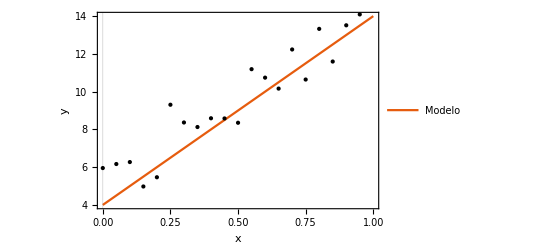

```mathematica
model[x_]:= 10 x + 4;
noise := RandomVariate[NormalDistribution[]];
data = Table[{x,model[x]+noise},{x,0,1,0.05}];
Plot[model[x],{x,0,1},Epilog->Point[data],PlotLegends->{"Modelo"}, PlotTheme->"Scientific", FrameLabel->{"x","y"}]
```

Se aplicará el algoritmo LMS sobre este conjunto de datos, y se monitoreará la función de costo por cada iteración.

El modelo que se encontró es: (θ0
θ1) = (3.45345
14.8885)

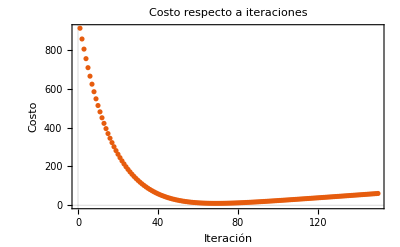

```mathematica
X = Table[{1,d[[1]]},{d,data}];
y = Table[d[[2]],{d,data}];

Module[{θ1,θ2,α,Θ},
θ1 = RandomReal[];
θ2 = RandomReal[];
α = 0.001;
Θ[θ1c_,θ2c_] := {{θ1},{θ2}};
hipotesis[X_,Θ_] := Flatten[Transpose[Θ].X][[1]];
Cost[X_,y_,θ_] := 1/2 Sum[(hipotesis[X[[i]],θ] - y[[i]])^2,{i,1,Length[y]}];
costs = {};
Do[
θ1  += α Sum[y[[i]] - hipotesis[X[[i]],Θ[θ1,θ2]] X[[i]][[1]],{i,1,Length[y]}];
θ2  += α Sum[y[[i]] - hipotesis[X[[i]],Θ[θ1,θ2]]X[[i]][[2]],{i,1,Length[y]}];
AppendTo[costs,Cost[X,y,Θ[θ1,θ2]]];
,{150}
];
Print["El modelo que se encontró es: (θ0
θ1) = ", MatrixForm[Θ[θ1,θ2]]];
Print[ListPlot[costs,PlotRange->Full, PlotTheme->"Scientific", FrameLabel->{"Iteración","Costo"}, PlotLabel->"Costo respecto a iteraciones"]];
]
```

Este algoritmo no converge del todo bien y según se observa en la gráfica del costo respecto a iteración se aleja del resultado correcto a partir de un número crítico de iteraciones. El problema con el algoritmo radica en que por cada iteración tiene que recorrer todo el conjunto de entrenamiento, de manera que cada cambio de θ es una operación costosa.

Algoritmo SGD

El algoritmo SGD (Stochastic gradient descent) consiste en actualizar los valores de θ con cada ejemplo de entrenamiento.  Con esta variación el algoritmo es

Loop[
	Para i=1 hasta m [
		θ_j = θ_j +α (y^(i)-h_θ(x^(i))) x_j^(i)  (para cada j)
	]
]

A continuación se muestra un ejemplo del algoritmo.

El modelo que se encontró es: (θ0
θ1) = (5.43917
8.44114)

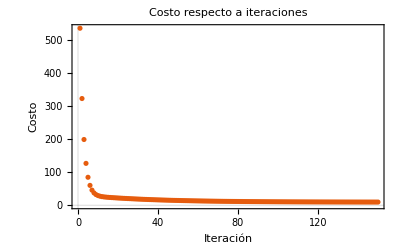

```mathematica
X = Table[{1,d[[1]]},{d,data}];
y = Table[d[[2]],{d,data}];

Module[{θ1,θ2,α,Θ},
θ1 = RandomReal[];
θ2 = RandomReal[];
α = 0.01;
Θ[θ1c_,θ2c_] := {{θ1},{θ2}};
hipotesis[X_,Θ_] := Flatten[Transpose[Θ].X][[1]];
Cost[X_,y_,θ_] := 1/2 Sum[(hipotesis[X[[i]],θ] - y[[i]])^2,{i,1,Length[y]}];
costs = {};
Do[
Do[
θ1  += α (y[[i]] - hipotesis[X[[i]],Θ[θ1,θ2]]) X[[i]][[1]];
θ2  += α (y[[i]] - hipotesis[X[[i]],Θ[θ1,θ2]]) X[[i]][[2]];
,{i,1,Length[y]}
];
AppendTo[costs,Cost[X,y,Θ[θ1,θ2]]];
,{150}
];
Print["El modelo que se encontró es: (θ0
θ1) = ", MatrixForm[Θ[θ1,θ2]]];
Print[ListPlot[costs,PlotRange->Full, PlotTheme->"Scientific", FrameLabel->{"Iteración","Costo"}, PlotLabel->"Costo respecto a iteraciones"]];
]
```

Solución analítica

Para obtener la solución analítica basta con construir la matriz de los costos y obtener la solución de θ para cuando el costo es mínimo. Es decir

J(θ) = 1/2(X θ - (y⃗))^T (X θ - y⃗),

y pidiendo que

∇_θ J(θ) = 0, 

entonces se obtiene

∇_θ J(θ) = X^T X θ - X^T y⃗  = 0,

cuya solución para θ es

θ = (X^T X)^-1 X^T y⃗ .

Esto es el método de mínimos cuadrados.